```mathematica
nF[ϵ_,β_]=(1+Exp[β(ϵ-μ)])^(-1);
μList = {0,1,3,5,10};
```

```mathematica
colors={{Black},{Red},{Blue},{Green},{Purple}};
colors2=Join[colors,Table[Append[colors[[i]],Dashed],{i,1,Length[colors]}]];
```

Part::pkspec1: The expression k cannot be used as a part specification.

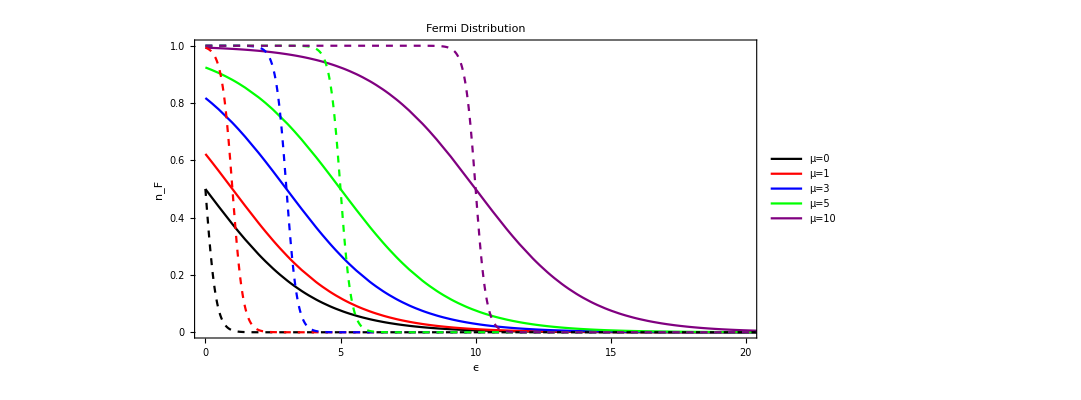

C:\Users\Sina\Google Drive\Classes\Spring 2021\Statistical Mechanics\HW5_p6aii(1)_image.png

```mathematica
β=0.5;
legend[k_]=Style[StringForm["μ=``",μList[[k]],β],20];
Plot[{Evaluate[nF[ϵ,β]/.μ->μList],Evaluate[nF[ϵ,10β]/.μ->μList]},{ϵ,0,100},PlotLabel->Style["Fermi Distribution",Black,28],PlotRange->{{0,20},{0,1}},PlotLegends->Placed[{legend[1], legend[2], legend[3], legend[4],legend[5]},{0.9,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["n_F",Black,28],None},{Style["ϵ",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->colors2]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW5_p6aii(1)_image.png",%,ImageResolution->500]
```

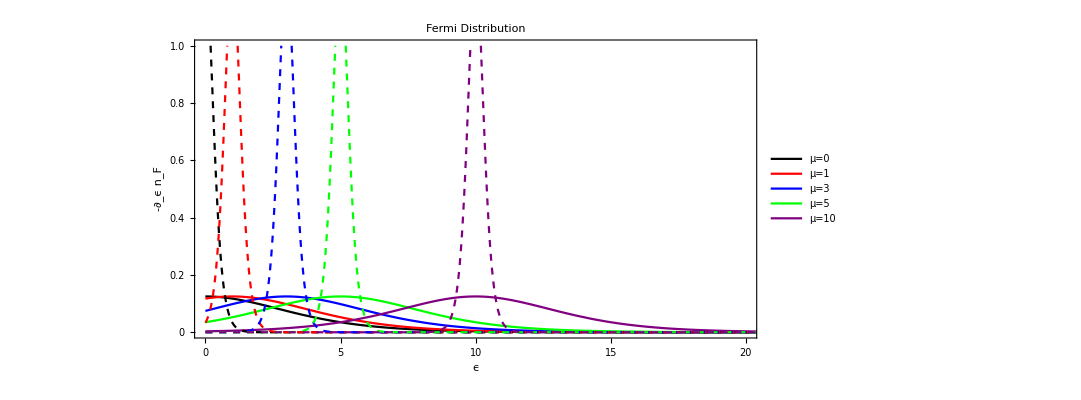

C:\Users\Sina\Google Drive\Classes\Spring 2021\Statistical Mechanics\HW5_p6aii(2)_image.png

```mathematica
Plot[{Evaluate[-D[nF[ϵ,β],ϵ]/.μ->μList],Evaluate[-D[nF[ϵ,10β],ϵ]/.μ->μList]},{ϵ,0,100},PlotLabel->Style["Fermi Distribution",Black,28],PlotRange->{{0,20},{0,1}},PlotLegends->Placed[{legend[1], legend[2], legend[3], legend[4],legend[5]},{0.9,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["-∂_ϵ n_F",Black,28],None},{Style["ϵ",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->colors2(*,Epilog->{{Black,Dotted,Line[{{μβList[[1]],0},{μβList[[1]],2}}]},{Red,Dotted,Line[{{μβList[[2]],0},{μβList[[2]],2}}]},{Blue,Dotted,Line[{{μβList[[3]],0},{μβList[[3]],2}}]},{Green,Dotted,Line[{{μβList[[4]],0},{μβList[[4]],2}}]},{Purple,Dotted,Line[{{μβList[[5]],0},{μβList[[5]],2}}]}}*)]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW5_p6aii(2)_image.png",%,ImageResolution->500]
```

```mathematica
UnitConvert[Sqrt[2Quantity[1,"ReducedPlanckConstant"^2]/(2 Quantity[1,"ElectronMass"])(3 Quantity[1,1/"Angstroms"^3]/(2 Pi^2))^(2/3)/Quantity[1,"ElectronMass"]]]
```

617804.409 m/s

```mathematica
Gamma[1]
```

1

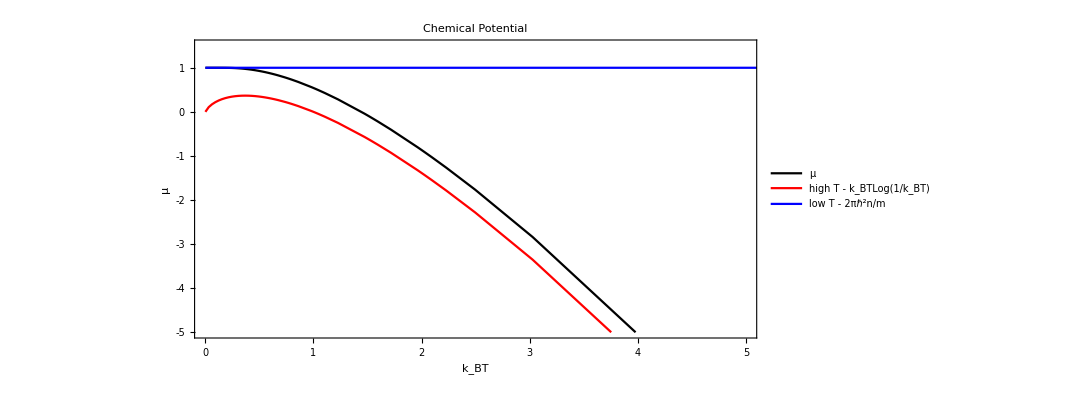

C:\Users\Sina\Google Drive\Classes\Spring 2021\Statistical Mechanics\HW5_p6ciii(1)_image.png

```mathematica
μ[βinverse_,α_] = βinverse Log[Exp[α/βinverse]-1];
Plot[{μ[β,1],-β Log[β],1},{β,0,100},PlotLabel->Style["Chemical Potential",Black,28],PlotRange->{{0,5},{-5,1.5}},PlotLegends->Placed[{Style["μ",20], Style["high T - k_BTLog(1/k_BT)",20], Style["low T - 2πℏ^2n/m",20], legend[4],legend[5]},{0.9,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["μ",Black,28],None},{Style["k_BT",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->colors2]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW5_p6ciii(1)_image.png",%,ImageResolution->500]
```